```mathematica
ClearAll["`*"]
Needs["EntropyGO`",NotebookDirectory[]<>"../src/EntropyGO.m"]
```

{{2,3}}

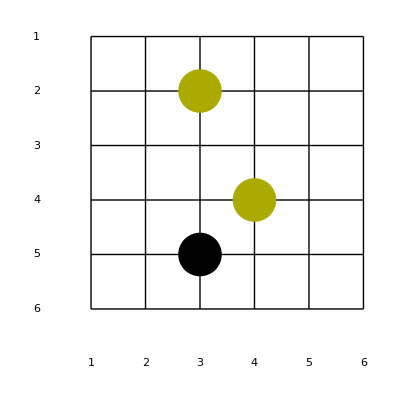

```mathematica
(*subα={GO`Private`α-> α,Abs[GO`Private`α]-> α};*)


Board= {{0,0,0,0,0,0},{0,-1,1,0,-1,0},{0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}};
board={{0,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,-1,0,0,0},{0,0,0,0,0,0}};

LoadBoard[board]
Draw[]
```

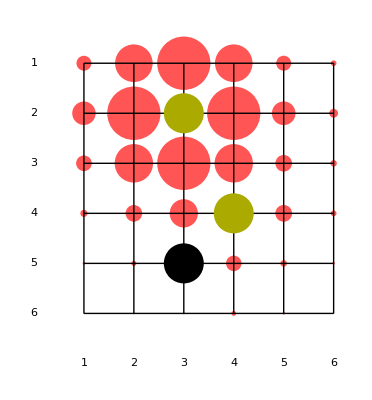

```mathematica
options={"boardPaths"-> True};
{boardInf,boardPaths}= BoardInfluenceFromGroup[Groups[1][[1]],1,options];

DrawTentacles[boardInf,3]
```

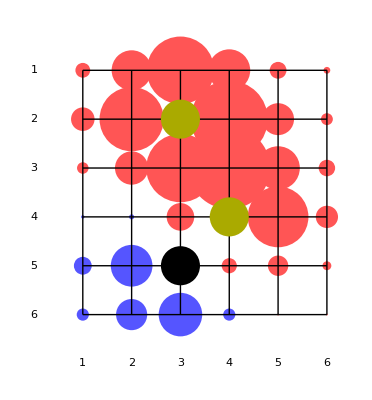

```mathematica
BoardOfLinksUDRL//MatrixForm;
Groups[1];
Groups[-1];

DrawTentacles[BoardInfluence,3]
```

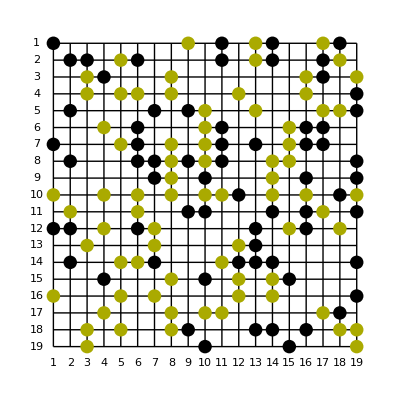

```mathematica
GenerateRandomBoard[19]
Draw[]
```

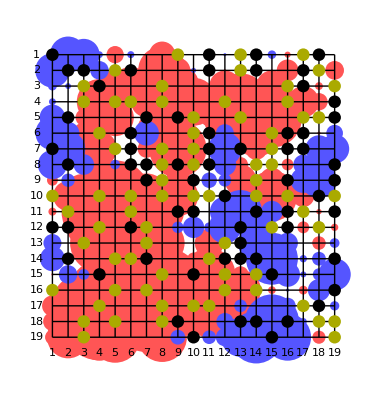

```mathematica
BoardInfluence~DrawTentacles~3

(*BoardInfluence  //RuntimeTools`Profile*)
```

```mathematica
(*Compilation attempts*)
ClearAll[AdjacentGroup,CAdjacentGroup]
AdjacentGroup[group_,coord_]:=  Intersection [{#[[1]]}&/@Position[group, Alternatives@@((coord+#)&/@listUDRL),2,4]];
CAdjacentGroup= Compile[{{group,_Integer,3},{coord,_Integer,1} },
  Intersection [{#[[1]]}&/@Flatten[Position[group,#,2,4]&/@(({2,2}+#)&/@listUDRL) ,1]]
];

Timing[AdjacentGroup[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}]][[1]]
Timing[CAdjacentGroup[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}]][[1]]

list[f_]:= Timing[Do[f[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}];,{#}]][[1]]&/@Range[100,2500,200]
ListPlot[{list[CAdjacentGroup],list[AdjacentGroup]} ]

<<CompiledFunctionTools`
CompilePrint[CAdjacentGroup];
```